```mathematica
ClearAll["Global`*"]
```

```mathematica
(*Define synchronization condition for driving strength*)
f[A_,m_,M_,n_]:= A / Sqrt[((4*m*M)/n)^2-1]
tg[O_]:=n*1000/(2*O)  
(*Calculate corresponding values for Bext*)
tau[M_, O_]:=n*1000/(2*M*O);
taul[tau_, l_]:=tau/l ;
Bext[tau_,l_]:=10000*l/(10.7*tau);(*Bext(tau) in units of Gauss. Value from Taminau group is 403G. For l=1 we get its minimum, which can be moved to stronger regimes by multiplication with l.*)
```

```mathematica
(*A is in units of kHz, thus driving strength is in units of kHz as well*)
(*A for 15N: 3030 kHz, A for 14N: 2160 kHz, A for exemplary strongly coupled 13C: 200 kHz and for weakly coupled: 25 kHz*)
(*in values list B1 is in units of Mhz*)
values = N[Table[{tg[f[A,m,M,n]],f[A,m,M,n]/1000,Bext[tau[M,f[A,m,M,n]],1],tau[M,f[A,m,M,n]],n,m,M},{n,1,9,2},{m,1,10,1},{M,2,10,2}]] ;
values= Flatten[values,2]/.A->200;
values=Select[values,Im[#[[1]]]<10^-6&];
values=Sort[values,Abs[#1[[3]]]<Abs[#2[[3]]]&];
values=Take[values,30];
values=Sort[values,Abs[#1[[1]]]<Abs[#2[[1]]]&]
```

{{198.73,0.0226437,9.4055,99.3652,9.,10.,2.},{199.233,0.0175674,9.38178,99.6165,7.,10.,2.},{199.609,0.0125245,9.3641,99.8045,5.,10.,2.},{199.859,0.00750528,9.35237,99.9297,3.,10.,2.},{199.984,0.0025002,9.34652,99.9922,1.,10.,2.},{359.991,0.00138892,10.3845,89.9978,1.,9.,4.},{399.367,0.0112678,9.36061,99.8417,9.,10.,4.},{399.617,0.00875839,9.35475,99.9043,7.,10.,4.},{399.805,0.00625305,9.35036,99.9512,5.,10.,4.},{399.93,0.00375066,9.34744,99.9824,3.,10.,4.},{399.992,0.00125002,9.34598,99.998,1.,10.,4.},{539.994,0.000925936,10.3843,89.999,1.,9.,6.},{599.578,0.00750528,9.35237,99.9297,9.,10.,6.},{599.745,0.00583582,9.34977,99.9575,7.,10.,6.},{599.87,0.00416757,9.34782,99.9783,5.,10.,6.},{599.953,0.0025002,9.34652,99.9922,3.,10.,6.},{599.995,0.000833341,9.34588,99.9991,1.,10.,6.},{719.996,0.000694449,10.3843,89.9995,1.,9.,8.},{799.684,0.00562723,9.34949,99.9604,9.,10.,8.},{799.809,0.00437605,9.34803,99.9761,7.,10.,8.},{799.902,0.00312538,9.34694,99.9878,5.,10.,8.},{799.965,0.00187508,9.34621,99.9956,3.,10.,8.},{799.996,0.000625003,9.34584,99.9995,1.,10.,8.},{899.969,0.00166672,10.3846,89.9969,3.,9.,10.},{899.997,0.000555558,10.3843,89.9997,1.,9.,10.},{999.747,0.00450114,9.34816,99.9747,9.,10.,10.},{999.847,0.00350054,9.34723,99.9847,7.,10.,10.},{999.922,0.0025002,9.34652,99.9922,5.,10.,10.},{999.972,0.00150004,9.34606,99.9972,3.,10.,10.},{999.997,0.000500002,9.34582,99.9997,1.,10.,10.}}

```mathematica
valuesgatetime = values[[All,{1,2}]];
valuesbext = values[[All, {1,3}]];
```

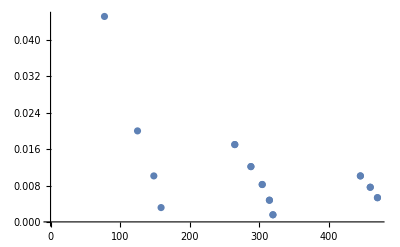

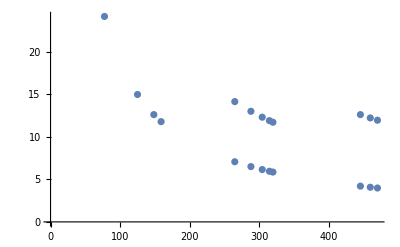

```mathematica
ListPlot[valuesgatetime]
ListPlot[valuesbext]
```

```mathematica
Export["gatetime25.dat",valuesgatetime]
Export["bext25.dat",valuesbext]
```

gatetime25.dat

bext25.dat